{0.,0.1,0.5,1.,2.}

{0.1,0.2,0.3,0.4,0.5,0.6,0.7}

(H̃)^u x=0.1 t=-{0.,0.1,0.5,1.,2.}

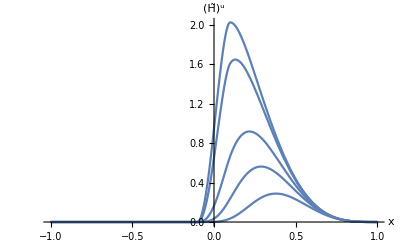

(H̃)^u t=-0.1 x=-{0.1,0.2,0.3,0.4,0.5,0.6,0.7}

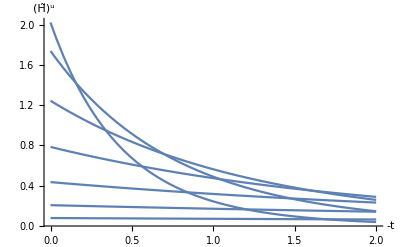

(H̃)^d x=0.1 t=-{0.,0.1,0.5,1.,2.}

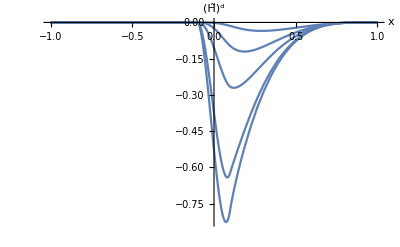

(Ẽ)^u x=0.1 t=-{0.,0.1,0.5,1.,2.}

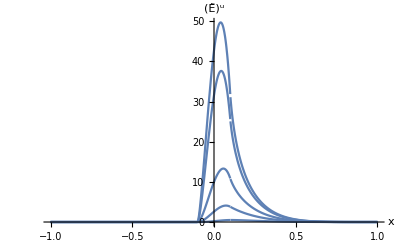

(Ẽ)^d x=0.1 t=-{0.,0.1,0.5,1.,2.}

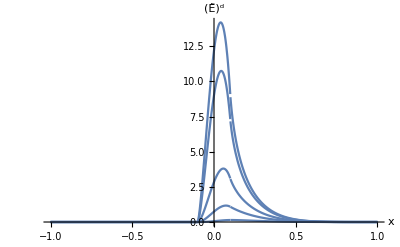

H_T^u x=0.1 t=-{0.,0.1,0.5,1.,2.}

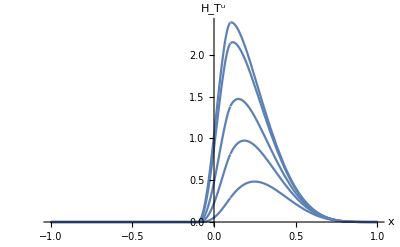

H_T^d x=0.1 t=-{0.,0.1,0.5,1.,2.}

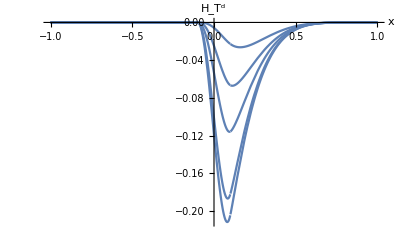

(Ē)_T^u x=0.1 t=-{0.,0.1,0.5,1.,2.}

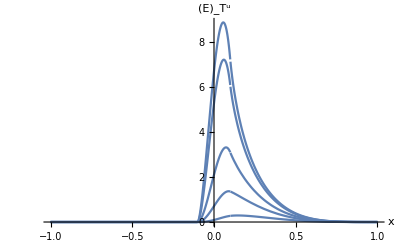

(Ē)_T^d x=0.1 t=-{0.,0.1,0.5,1.,2.}

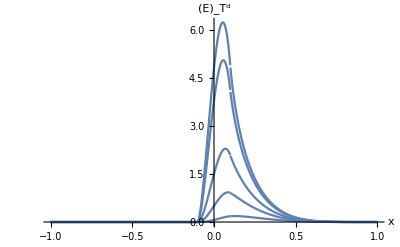

(H̃)^u t=-0.0

-Graphics3D-

(H̃)^d t=-0.0

-Graphics3D-

(Ẽ)^u t=-0.0

-Graphics3D-

(Ẽ)^d t=-0.0

-Graphics3D-

H_T^u t=-0.0

-Graphics3D-

H_T^d t=-0.0

-Graphics3D-

(Ē)_T^u t=-0.0

-Graphics3D-

(Ē)_T^d t=-0.0

-Graphics3D-

```mathematica
listt={0.,0.1,0.5,1.,2.}
listx={0.1,0.2,0.3,0.4,0.5,0.6,0.7}
Print["(H̃)^u x=0.1 t=-",listt]
Show[Plot[Htildeu[x,0.1,-#],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(H̃)^u"}]&/@listt]
Print["(H̃)^u t=-0.1 x=-",listx]
Show[Plot[Htildeu[#,0.1,-t],{t,.0,2.0},PlotRange->All,AxesLabel->{"-t","(H̃)^u"}]&/@listx]
Print["(H̃)^d x=0.1 t=-",listt]
Show[Plot[Htilded[x,0.1,-#],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(H̃)^d"}]&/@listt]
Print["(Ẽ)^u x=0.1 t=-",listt]
Show[Plot[Etildeu[x,0.1,-#],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ẽ)^u"}]&/@listt]
Print["(Ẽ)^d x=0.1 t=-",listt]
Show[Plot[Etilded[x,0.1,-#],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ẽ)^d"}]&/@listt]
Print["H_T^u x=0.1 t=-",listt]
Show[Plot[HTu[x,0.1,-#],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","H_T^u"}]&/@listt]
Print["H_T^d x=0.1 t=-",listt]
Show[Plot[HTd[x,0.1,-#],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","H_T^d"}]&/@listt]
Print["(Ē)_T^u x=0.1 t=-",listt]
Show[Plot[EbarTu[x,0.1,-#],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ē)_T^u"}]&/@listt]
Print["(Ē)_T^d x=0.1 t=-",listt]
Show[Plot[EbarTd[x,0.1,-#],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ē)_T^d"}]&/@listt]

Print["(H̃)^u t=-0.0"]
Plot3D[Htildeu[x,xi,-0.00],{x,-1.0,1.0},{xi,.01,1.0},AxesLabel->{"x","ξ","(H̃)^u"},PlotRange->All,ColorFunction->"DarkRainbow"]
Print["(H̃)^d t=-0.0"]
Plot3D[Htilded[x,xi,-0.00],{x,-1.0,1.0},{xi,.01,1.0},AxesLabel->{"x","ξ","(H̃)^u"},PlotRange->All,ColorFunction->"DarkRainbow"]

Print["(Ẽ)^u t=-0.0"]
Plot3D[Etildeu[x,xi,-0.00],{x,-1.0,1.0},{xi,.01,1.0},AxesLabel->{"x","ξ","(Ẽ)^u"},PlotRange->All,ColorFunction->"DarkRainbow"]

Print["(Ẽ)^d t=-0.0"]
Plot3D[Etilded[x,xi,-0.00],{x,-1.0,1.0},{xi,.01,1.0},AxesLabel->{"x","ξ","(Ẽ)^d"},PlotRange->All,ColorFunction->"DarkRainbow"]

Print["H_T^u t=-0.0"]

Plot3D[HTu[x,xi,-0.00],{x,-1.0,1.0},{xi,.01,1.0},AxesLabel->{"x","ξ","H_T^u"},PlotRange->All,ColorFunction->"DarkRainbow"]
Print["H_T^d t=-0.0"]
Plot3D[HTd[x,xi,-0.0],{x,-1.0,1.0},{xi,.01,1.0},AxesLabel->{"x","ξ","H_T^d"},PlotRange->All,ColorFunction->"DarkRainbow"]
Print["(Ē)_T^u t=-0.0"]

Plot3D[EbarTu[x,xi,-0.00],{x,-1.0,1.0},{xi,.01,1.0},AxesLabel->{"x","ξ","(Ē)_T^u"},PlotRange->All,ColorFunction->"DarkRainbow"]
Print["(Ē)_T^d t=-0.0"]
Plot3D[EbarTd[x,xi,-0.0],{x,-1.0,1.0},{xi,.01,1.0},AxesLabel->{"x","ξ","(Ē)_T^d"},PlotRange->All,ColorFunction->"DarkRainbow"]
```

```mathematica
"
```